-(-1)^(3/4) ⅇ^(-1/2 ⅈ n π+ⅈ Y) √(2/π) √(1/Y)

Cos[(n π)/2+Y Sin[θin]]

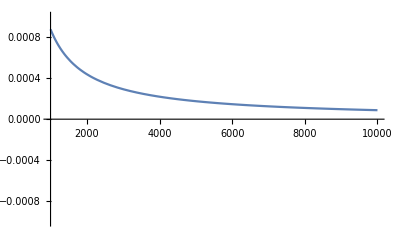

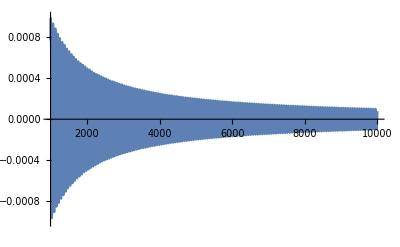

```mathematica
ClearAll[hankeln]

$Assumptions={X>0,Y>0,n∈Integers,θin∈Reals,Y0>0};
hankeln[Y_] = Normal@Series[
HankelH1[n,R]/.R->Normal@Series[√(X^2+Y^2),{Y,∞,0}]
,{Y,∞,1}]
angular[Y_] =Normal@Series[
Cos[Y Sin[θin]+n arc]/.arc->Normal@Series[ ArcTan[X,Y],{Y,∞,1}]
,{X,0,0}]


Plot[
Abs[HankelH1[n,Sqrt[X^2+Y^2]]- hankeln[Y]]/(Abs@HankelH1[n,Sqrt[X^2+Y^2]])/.{n->1,X->1,θin-> 0.1}
,{Y,1000.,10000.1},PlotRange-> 0.001]
Plot[
Cos[Y Sin[θin]+n ArcTan[X,Y]]-angular[Y]/.{n->1,X->1,θin-> 0.1}
,{Y,1000.,10000.1},PlotRange-> 0.001]
(*Plot[Cos[Y Sin[θin]+n ArcTan[X,Y]]-(Cos[Y Sin[θin]+n π/2]+n X/Y Sin[Y Sin[θin]+n π/2]) /.{n->1,X->1,θin-> 0.1},{Y,10.,1000.1}];*)
```

```mathematica
(*Integrate[hankeln[Y]Cos[Y Sin[θin]+n π/2]+n X/Y Sin[Y Sin[θin]+n π/2],{Y,Y0,∞}]
 Series[%,{Y0,∞,1}]//Normal//FullSimplify
*)
(*int=Integrate[hankeln[Y]Cos[Y Sin[θin]+n π/2] ,{Y,Y0,∞}]
Bapp =  Series[%,{Y0,∞,1}]//Normal//FullSimplify;*)
```

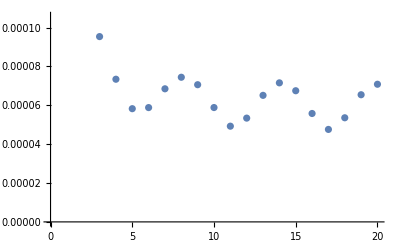

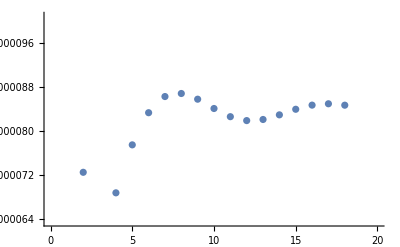

```mathematica
ClearAll[F,Bapp,B,Bend,error1,error2]

k=1.0;
a12 = 1.0;
(*Bapp[n_,X_,Y0_,θin_:0.0]=2.0(-1.0)^n 1/(√π √Y0)(1/2+ⅈ/2) (-1)^n ⅇ^(-ⅈ Y0 (-1+Sin[θin])) Sec[θin] (Sec[θin]+(-1)^n ⅇ^(2 ⅈ Y0 Sin[θin]) (Sec[θin]-Tan[θin])+Tan[θin]);*)

Bapp[n_,X_,Y0_,θin_:0.0]=(1+ⅈ)/(√(π Y0) Cos[θin]^2)  ⅇ^(ⅈ  Y0 (1-Sin[θin])) (1+(-1)^n ⅇ^(2 ⅈ Y0 Sin[θin]) (1-Sin[θin])+Sin[θin]);
F[n_,X_,Y_]:= (-1)^n Exp[ⅈ n ArcTan[X,Y] ]HankelH1[n,Sqrt[X^2+Y^2]]

B[n_,X_,θin_:0.0]:=NIntegrate[Boole[Y^2>k^2a12^2 - X^2 ] ⅇ^(ⅈ Y Sin[θin])F[n,X,Y],{Y,-∞,∞}]
Bend[n_,X_,Y0_,θin_:0.0]:=NIntegrate[Boole[Y^2>Y0^2 ] ⅇ^(ⅈ Y Sin[θin])F[n,X,Y],{Y,-∞,∞}]

error0[Y0_]:=(
args = {1,0.0,Y0,0.8};
B0=Abs@B[args[[1]],args[[2]],args[[4]]];
Abs[Bend@@args - Bapp@@args]/B0
)
error1[Y0_]:=(
args = {0,1.0,Y0,0.1};
B0=Abs@B[args[[1]],args[[2]],args[[4]]];
Abs[Bend@@args - Bapp@@args]/B0
)

ListPlot[error0/@Range[100.,10000.,500.]]
ListPlot[error1/@Range[100.,10000.,500.]]
```

```mathematica
F[n_,X_,Y_]:= (-1)^n Exp[ⅈ n ArcTan[X,Y] ]HankelH1[n,Sqrt[X^2+Y^2]]

S[n_,X_,θin_:0.0]:=NIntegrate[ⅇ^(ⅈ Y Sin[θin])F[n,X,Y],{Y,-∞,∞}]
S2[n_,X_,θin_:0.0] = 2 ⅈ^n ⅇ^(-ⅈ n θin)/Cos[θin] ⅇ^(ⅈ X Cos[θin])
S2[#,0.2]-S[#,0.2]&/@Range[0,3] 

S2[#,20.,0.3]-S[#,20.,0.3]&/@Range[0,3]
```

2 ⅈ^n ⅇ^(-ⅈ n θin+ⅈ X Cos[θin]) Sec[θin]

{-1.57274×10^-11+6.18905×10^-12 ⅈ,1.19282×10^-10-5.23253×10^-11 ⅈ,-1.48841×10^-11+9.94538×10^-13 ⅈ,-7.5534×10^-13+1.85718×10^-12 ⅈ}

{2.02895×10^-11-9.13269×10^-13 ⅈ,-6.54543×10^-12-8.36131×10^-12 ⅈ,9.92317×10^-13+2.1219×10^-11 ⅈ,-7.61102×10^-12-1.59772×10^-11 ⅈ}